## LJ Potential Function

```mathematica
Subr=r0+4(r1−r0)((z/L)^2)
Subρ=Sqrt[(r^2)(δ^2)+(z−z0)^2]/.{r->Subr}
SubA=4ϵ σ^6
SubB=4ϵ σ^12
```

r0+(4 (-r0+r1) z^2)/L^2

√((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)

4 ϵ σ^6

4 ϵ σ^12

```mathematica
Phi[ϵ,σ,δ,z]=(r^2)δ(−A(ρ^(−6))+B(ρ^(−12)))/.{A->SubA,B->SubB,ρ->Subρ,r->Subr}
```

(r0+(4 (-r0+r1) z^2)/L^2)^2 δ (-(4 ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^6))

## Partial Derivatives of LJ Potential

```mathematica
Phigrad=Grad[Phi[ϵ,σ,δ,z],{δ,z}]
```

{(r0+(4 (-r0+r1) z^2)/L^2)^2 δ ((24 (r0+(4 (-r0+r1) z^2)/L^2)^2 δ ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^4)-(48 (r0+(4 (-r0+r1) z^2)/L^2)^2 δ ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^7))+(r0+(4 (-r0+r1) z^2)/L^2)^2 (-(4 ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^6)),(r0+(4 (-r0+r1) z^2)/L^2)^2 δ ((12 (2 (z-z0)+(16 (-r0+r1) z (r0+(4 (-r0+r1) z^2)/L^2) δ^2)/L^2) ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^4)-(24 (2 (z-z0)+(16 (-r0+r1) z (r0+(4 (-r0+r1) z^2)/L^2) δ^2)/L^2) ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^7))+(16 (-r0+r1) z (r0+(4 (-r0+r1) z^2)/L^2) δ (-(4 ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^6)))/L^2}

```mathematica
Phipartialδ=Phigrad[[1]]/.{r0->Subr0,r1->Subr1,L->SubL,z0->Subz0}
Phipartialz=Phigrad[[2]]/.{r0->Subr0,r1->Subr1,L->SubL,z0->Subz0}
```

(1+z^2/25)^2 δ ((24 (1+z^2/25)^2 δ ϵ σ^6)/(((5+z)^2+(1+z^2/25)^2 δ^2)^4)-(48 (1+z^2/25)^2 δ ϵ σ^12)/(((5+z)^2+(1+z^2/25)^2 δ^2)^7))+(1+z^2/25)^2 (-(4 ϵ σ^6)/(((5+z)^2+(1+z^2/25)^2 δ^2)^3)+(4 ϵ σ^12)/(((5+z)^2+(1+z^2/25)^2 δ^2)^6))

(1+z^2/25)^2 δ ((12 (2 (5+z)+4/25 z (1+z^2/25) δ^2) ϵ σ^6)/(((5+z)^2+(1+z^2/25)^2 δ^2)^4)-(24 (2 (5+z)+4/25 z (1+z^2/25) δ^2) ϵ σ^12)/(((5+z)^2+(1+z^2/25)^2 δ^2)^7))+4/25 z (1+z^2/25) δ (-(4 ϵ σ^6)/(((5+z)^2+(1+z^2/25)^2 δ^2)^3)+(4 ϵ σ^12)/(((5+z)^2+(1+z^2/25)^2 δ^2)^6))

## Force

```mathematica
Force=-Grad[Phi[ϵ,σ,δ,z],{δ,z}]
```

{-(r0+(4 (-r0+r1) z^2)/L^2)^2 δ ((24 (r0+(4 (-r0+r1) z^2)/L^2)^2 δ ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^4)-(48 (r0+(4 (-r0+r1) z^2)/L^2)^2 δ ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^7))-(r0+(4 (-r0+r1) z^2)/L^2)^2 (-(4 ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^6)),-(r0+(4 (-r0+r1) z^2)/L^2)^2 δ ((12 (2 (z-z0)+(16 (-r0+r1) z (r0+(4 (-r0+r1) z^2)/L^2) δ^2)/L^2) ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^4)-(24 (2 (z-z0)+(16 (-r0+r1) z (r0+(4 (-r0+r1) z^2)/L^2) δ^2)/L^2) ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^7))-(16 (-r0+r1) z (r0+(4 (-r0+r1) z^2)/L^2) δ (-(4 ϵ σ^6)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^3)+(4 ϵ σ^12)/(((z-z0)^2+(r0+(4 (-r0+r1) z^2)/L^2)^2 δ^2)^6)))/L^2}

## Absolute minima for different values of ϵ and σ, starting with equal pairs such as (ϵ,σ)=(1,1), (2,2), ...

```mathematica
Subϵ=0;
Subσ=0;

minimumPhiArray={};
minimumPhiArrayPlot={};
δforminPhiArray={};
zforminPhiArray={};


For[i=0,i<=10,i++,
Clear[Phipartialδ,Phipartialz,criticalpts,phisimplified,phievaluated];

Subϵ++;
Subσ++;

Phipartialδ=Phigrad[[1]]/.{r0->Subr0,r1->Subr1,L->SubL,z0->Subz0,ϵ->Subϵ,σ->Subσ};
Phipartialz=Phigrad[[2]]/.{r0->Subr0,r1->Subr1,L->SubL,z0->Subz0,ϵ->Subϵ,σ->Subσ};
criticalpts=NSolve[{Phipartialδ==0,Phipartialz==0},{δ,z},Reals];

phisimplified=Phi[ϵ,σ,δ,z]/.{r0->Subr0,r1->Subr1,L->SubL,z0->Subz0,ϵ->Subϵ,σ->Subσ};
phievaluated={};

For[i=1,i<=Length[criticalpts],i++,
phievaluated=AppendTo[phievaluated,phisimplified/.criticalpts[[i]]];
];

minimumPhiArray=AppendTo[minimumPhiArray,{Subϵ,Subσ,Min[phievaluated]}];
criticalptsIndex=Position[phievaluated,Min[phievaluated]];
solδ=criticalpts[[criticalptsIndex[[1,1]],1]]/.Rule->List;
solz=criticalpts[[criticalptsIndex[[1,1]],2]]/.Rule->List;
δforminPhiArray=AppendTo[δforminPhiArray,{Subϵ,Subσ,Part[solδ,2]}];
zforminPhiArray=AppendTo[zforminPhiArray,{Subϵ,Subσ,Part[solz,2]}];


Print[criticalpts,phievaluated,"\n",Min[phievaluated],"\n\n"]

]
Print[minimumPhiArray,"\n\n",δforminPhiArray,"\n\n",zforminPhiArray]
```

{{δ→0,z→-4.},{δ→0,z→-6.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-2.32017,2.32017}
-2.32017

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→-0.886218,z→-5.88056},{δ→0.886218,z→-5.88056}}{0.,0.,9.94877,-9.94877}
-9.94877

{{δ→0,z→-8.},{δ→1.06653,z→-6.71068},{δ→-1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,-24.7199,24.7199,0.}
-24.7199

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,-49.3308,-49.3308,49.3308,49.3308,0.}
-49.3308

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-87.1568,87.1568,0,0}
-87.1568

{{δ→0,z→-11.},{δ→-1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→0,z→1.}}{0.,142.181,142.181,-142.181,-142.181,0.}
-142.181

{{δ→0,z→-12.},{δ→1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→0,z→2.}}{0.,-218.969,-218.969,218.969,218.969,0.}
-218.969

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,322.663,-322.663,0.}
-322.663

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→-1.01796,z→-12.4799},{δ→1.01796,z→-12.4799},{δ→4.73289,z→3.23863},{δ→-4.73289,z→3.23863},{δ→0,z→4.}}{0.,-77.4502,77.4502,458.976,-458.976,-79.8696,79.8696,0.}
-458.976

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→-0.975928,z→-13.463},{δ→0.975928,z→-13.463},{δ→0,z→5.},{δ→-3.67776,z→4.7405},{δ→3.67776,z→4.7405}}{-99.9777,99.9777,0.,634.194,-634.194,0.,118.581,-118.581}
-634.194

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→3.06762,z→5.9929},{δ→-3.06762,z→5.9929}}{-124.283,124.283,0.,0.,-855.169,855.169,0.,-174.671,174.671}
-855.169

{{1,1,-2.32017},{2,2,-9.94877},{3,3,-24.7199},{4,4,-49.3308},{5,5,-87.1568},{6,6,-142.181},{7,7,-218.969},{8,8,-322.663},{9,9,-458.976},{10,10,-634.194},{11,11,-855.169}}

{{1,1,0.530154},{2,2,0.886218},{3,3,1.06653},{4,4,1.13754},{5,5,1.14989},{6,6,1.13212},{7,7,1.09942},{8,8,1.05991},{9,9,1.01796},{10,10,0.975928},{11,11,0.935074}}

{{1,1,-5.248},{2,2,-5.88056},{3,3,-6.71068},{4,4,-7.6253},{5,5,-8.57604},{6,6,-9.54329},{7,7,-10.5186},{8,8,-11.4982},{9,9,-12.4799},{10,10,-13.463},{11,11,-14.4466}}

```mathematica
ListPointPlot3D[minimumPhiArray]
```

-Graphics3D-

```mathematica
ListPointPlot3D[δforminPhiArray]
```

-Graphics3D-

```mathematica
ListPointPlot3D[zforminPhiArray]
```

-Graphics3D-

## Absolute minima for various values of ϵ and σ NOTE: There is an error in the loop where only the first iteration is up to 11 and the later ones go up to 12 for some reason. This is not happening with the residual plots which is good, but I need to fix it here so that things are consistent.

```mathematica
Subϵ=0;
Subσ=0;

minimumPhiArray={};
minimumPhiArrayPlot={};
δforminPhiArray={};
zforminPhiArray={};

For[n=0,n<=10,n++,


Clear[Phipartialδ,Phipartialz,criticalpts,phisimplified,phievaluated];

Subϵ++;
Subσ=0;

For[i=0,i<=10,i++,

Subσ++;

Phipartialδ=Phigrad[[1]]/.{r0->Subr0,r1->Subr1,L->SubL,z0->Subz0,ϵ->Subϵ,σ->Subσ};
Phipartialz=Phigrad[[2]]/.{r0->Subr0,r1->Subr1,L->SubL,z0->Subz0,ϵ->Subϵ,σ->Subσ};
criticalpts=NSolve[{Phipartialδ==0,Phipartialz==0},{δ,z},Reals];

phisimplified=Phi[ϵ,σ,δ,z]/.{r0->Subr0,r1->Subr1,L->SubL,z0->Subz0,ϵ->Subϵ,σ->Subσ};
phievaluated={};

For[i=1,i<=Length[criticalpts],i++,
phievaluated=AppendTo[phievaluated,phisimplified/.criticalpts[[i]]];
];

minimumPhiArray=AppendTo[minimumPhiArray,{Subϵ,Subσ,Min[phievaluated]}];
criticalptsIndex=Position[phievaluated,Min[phievaluated]];
solδ=criticalpts[[criticalptsIndex[[1,1]],1]]/.Rule->List;
solz=criticalpts[[criticalptsIndex[[1,1]],2]]/.Rule->List;
δforminPhiArray=AppendTo[δforminPhiArray,{Subϵ,Subσ,Part[solδ,2]}];
zforminPhiArray=AppendTo[zforminPhiArray,{Subϵ,Subσ,Part[solz,2]}];


Print[criticalpts,phievaluated,"\n",{Subϵ,Subσ,Min[phievaluated]},"\n\n"]

]
]
Print[minimumPhiArray,"\n\n",δforminPhiArray,"\n\n",zforminPhiArray]
```

{{δ→0,z→-4.},{δ→0,z→-6.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-2.32017,2.32017}
{1,1,-2.32017}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→0.886218,z→-5.88056},{δ→-0.886218,z→-5.88056}}{0.,0.,-4.97439,4.97439}
{1,2,-4.97439}

{{δ→0,z→-8.},{δ→1.06653,z→-6.71068},{δ→-1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,-8.23997,8.23997,0.}
{1,3,-8.23997}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,12.3327,12.3327,-12.3327,-12.3327,0.}
{1,4,-12.3327}

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-17.4314,17.4314,0,0}
{1,5,-17.4314}

{{δ→0,z→-11.},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→0,z→1.}}{0.,23.6968,-23.6968,23.6968,-23.6968,0.}
{1,6,-23.6968}

{{δ→0,z→-12.},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→0,z→2.}}{0.,31.2812,-31.2812,-31.2812,31.2812,0.}
{1,7,-31.2812}

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,40.3328,-40.3328,0.}
{1,8,-40.3328}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→1.01796,z→-12.4799},{δ→-1.01796,z→-12.4799},{δ→-4.73289,z→3.23863},{δ→4.73289,z→3.23863},{δ→0,z→4.}}{0.,-8.60558,8.60558,-50.9973,50.9973,8.8744,-8.8744,0.}
{1,9,-50.9973}

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→0.975928,z→-13.463},{δ→-0.975928,z→-13.463},{δ→0,z→5.},{δ→3.67776,z→4.7405},{δ→-3.67776,z→4.7405}}{-9.99777,9.99777,0.,-63.4194,63.4194,0.,-11.8581,11.8581}
{1,10,-63.4194}

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→-3.06762,z→5.9929},{δ→3.06762,z→5.9929}}{-11.2985,11.2985,0.,0.,-77.7426,77.7426,0.,15.8792,-15.8792}
{1,11,-77.7426}

{{δ→0,z→-6.},{δ→0,z→-4.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-4.64033,4.64033}
{2,1,-4.64033}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→-0.886218,z→-5.88056},{δ→0.886218,z→-5.88056}}{0.,0.,9.94877,-9.94877}
{2,2,-9.94877}

{{δ→0,z→-8.},{δ→1.06653,z→-6.71068},{δ→-1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,-16.4799,16.4799,0.}
{2,3,-16.4799}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,24.6654,-24.6654,-24.6654,24.6654,0.}
{2,4,-24.6654}

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-34.8627,34.8627,0,0}
{2,5,-34.8627}

{{δ→0,z→-11.},{δ→1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→0,z→1.}}{0.,-47.3935,-47.3935,47.3935,47.3935,0.}
{2,6,-47.3935}

{{δ→0,z→-12.},{δ→-1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→0,z→2.}}{0.,62.5624,62.5624,-62.5624,-62.5624,0.}
{2,7,-62.5624}

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,80.6656,-80.6656,0.}
{2,8,-80.6656}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→-1.01796,z→-12.4799},{δ→1.01796,z→-12.4799},{δ→4.73289,z→3.23863},{δ→-4.73289,z→3.23863},{δ→0,z→4.}}{0.,-17.2112,17.2112,101.995,-101.995,-17.7488,17.7488,0.}
{2,9,-101.995}

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→-0.975928,z→-13.463},{δ→0.975928,z→-13.463},{δ→0,z→5.},{δ→-3.67776,z→4.7405},{δ→3.67776,z→4.7405}}{-19.9955,19.9955,0.,126.839,-126.839,0.,23.7162,-23.7162}
{2,10,-126.839}

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→3.06762,z→5.9929},{δ→-3.06762,z→5.9929}}{-22.597,22.597,0.,-155.485,155.485,0.,-31.7584,31.7584}
{2,11,-155.485}

{{δ→-12.5212,z→0.429737},{δ→12.5212,z→0.429737},{δ→0,z→-17.},{δ→-0.896033,z→-15.4307},{δ→0.896033,z→-15.4307},{δ→-2.64045,z→7.15236},{δ→2.64045,z→7.15236},{δ→2.64045,z→7.15236},{δ→0,z→7.}}{25.1084,-25.1084,0.,188.221,-188.221,42.056,-42.056,-42.056,0.}
{2,12,-188.221}

{{δ→0,z→-6.},{δ→0,z→-4.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-6.9605,6.9605}
{3,1,-6.9605}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→0.886218,z→-5.88056},{δ→-0.886218,z→-5.88056}}{0.,0.,-14.9232,14.9232}
{3,2,-14.9232}

{{δ→0,z→-8.},{δ→1.06653,z→-6.71068},{δ→-1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,-24.7199,24.7199,0.}
{3,3,-24.7199}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,36.9981,-36.9981,36.9981,-36.9981,0.}
{3,4,-36.9981}

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-52.2941,52.2941,0,0}
{3,5,-52.2941}

{{δ→0,z→-11.},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→0,z→1.}}{0.,-71.0903,71.0903,-71.0903,71.0903,0.}
{3,6,-71.0903}

{{δ→0,z→-12.},{δ→-1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→0,z→2.}}{0.,93.8437,93.8437,-93.8437,-93.8437,0.}
{3,7,-93.8437}

{{δ→0,z→-13.},{δ→1.05991,z→-11.4982},{δ→-1.05991,z→-11.4982},{δ→0,z→3.}}{0.,-120.998,120.998,0.}
{3,8,-120.998}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→-1.01796,z→-12.4799},{δ→1.01796,z→-12.4799},{δ→4.73289,z→3.23863},{δ→-4.73289,z→3.23863},{δ→0,z→4.}}{0.,-25.8167,25.8167,152.992,-152.992,-26.6232,26.6232,0.}
{3,9,-152.992}

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→0.975928,z→-13.463},{δ→-0.975928,z→-13.463},{δ→0,z→5.},{δ→3.67776,z→4.7405},{δ→-3.67776,z→4.7405}}{-29.9933,29.9933,0.,-190.258,190.258,0.,-35.5743,35.5743}
{3,10,-190.258}

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→-0.935074,z→-14.4466},{δ→0.935074,z→-14.4466},{δ→0,z→6.},{δ→3.06762,z→5.9929},{δ→-3.06762,z→5.9929}}{-33.8954,33.8954,0.,233.228,-233.228,0.,-47.6375,47.6375}
{3,11,-233.228}

{{δ→-12.5212,z→0.429737},{δ→12.5212,z→0.429737},{δ→12.5212,z→0.429737},{δ→0,z→-17.},{δ→0,z→-17.},{δ→-0.896033,z→-15.4307},{δ→0.896033,z→-15.4307},{δ→-2.64045,z→7.15236},{δ→2.64045,z→7.15236},{δ→0,z→7.}}{37.6626,-37.6626,-37.6626,0.,0.,282.331,-282.331,63.084,-63.084,0.}
{3,12,-282.331}

{{δ→0,z→-6.},{δ→0,z→-4.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-9.28066,9.28066}
{4,1,-9.28066}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→-0.886218,z→-5.88056},{δ→0.886218,z→-5.88056}}{0.,0.,19.8975,-19.8975}
{4,2,-19.8975}

{{δ→0,z→-8.},{δ→1.06653,z→-6.71068},{δ→-1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,-32.9599,32.9599,0.}
{4,3,-32.9599}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,-49.3308,-49.3308,49.3308,49.3308,0.}
{4,4,-49.3308}

{{δ→0,z→-10.},{δ→-1.14989,z→-8.57604},{δ→1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,69.7254,-69.7254,0,0}
{4,5,-69.7254}

{{δ→0,z→-11.},{δ→-1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→0,z→1.}}{0.,94.787,94.787,-94.787,-94.787,0.}
{4,6,-94.787}

{{δ→0,z→-12.},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→0,z→2.}}{0.,125.125,-125.125,125.125,-125.125,0.}
{4,7,-125.125}

{{δ→0,z→-13.},{δ→1.05991,z→-11.4982},{δ→-1.05991,z→-11.4982},{δ→0,z→3.}}{0.,-161.331,161.331,0.}
{4,8,-161.331}

{{δ→0,z→-14.},{δ→-7.91083,z→1.16827},{δ→7.91083,z→1.16827},{δ→1.01796,z→-12.4799},{δ→-1.01796,z→-12.4799},{δ→4.73289,z→3.23863},{δ→-4.73289,z→3.23863},{δ→0,z→4.}}{0.,34.4223,-34.4223,-203.989,203.989,-35.4976,35.4976,0.}
{4,9,-203.989}

{{δ→-9.72248,z→0.743038},{δ→9.72248,z→0.743038},{δ→0,z→-15.},{δ→0.975928,z→-13.463},{δ→-0.975928,z→-13.463},{δ→0,z→5.},{δ→3.67776,z→4.7405},{δ→-3.67776,z→4.7405}}{39.9911,-39.9911,0.,-253.677,253.677,0.,-47.4324,47.4324}
{4,10,-253.677}

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→-3.06762,z→5.9929},{δ→3.06762,z→5.9929}}{-45.1939,45.1939,0.,-310.97,310.97,0.,63.5167,-63.5167}
{4,11,-310.97}

{{δ→-12.5212,z→0.429737},{δ→12.5212,z→0.429737},{δ→12.5212,z→0.429737},{δ→0,z→-17.},{δ→-0.896033,z→-15.4307},{δ→0.896033,z→-15.4307},{δ→-2.64045,z→7.15236},{δ→2.64045,z→7.15236},{δ→0,z→7.}}{50.2168,-50.2168,-50.2168,0.,376.441,-376.441,84.112,-84.112,0.}
{4,12,-376.441}

{{δ→0,z→-4.},{δ→0,z→-6.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-11.6008,11.6008}
{5,1,-11.6008}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→0.886218,z→-5.88056},{δ→-0.886218,z→-5.88056}}{0.,0.,-24.8719,24.8719}
{5,2,-24.8719}

{{δ→0,z→-8.},{δ→1.06653,z→-6.71068},{δ→-1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,-41.1999,41.1999,0.}
{5,3,-41.1999}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,61.6636,61.6636,-61.6636,-61.6636,0.}
{5,4,-61.6636}

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-87.1568,87.1568,0,0}
{5,5,-87.1568}

{{δ→0,z→-11.},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→0,z→1.}}{0.,118.484,-118.484,118.484,-118.484,0.}
{5,6,-118.484}

{{δ→0,z→-12.},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→0,z→2.}}{0.,156.406,-156.406,-156.406,156.406,0.}
{5,7,-156.406}

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,201.664,-201.664,0.}
{5,8,-201.664}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→1.01796,z→-12.4799},{δ→-1.01796,z→-12.4799},{δ→-4.73289,z→3.23863},{δ→4.73289,z→3.23863},{δ→0,z→4.}}{0.,-43.0279,43.0279,-254.987,254.987,44.372,-44.372,0.}
{5,9,-254.987}

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→0.975928,z→-13.463},{δ→-0.975928,z→-13.463},{δ→0,z→5.},{δ→3.67776,z→4.7405},{δ→-3.67776,z→4.7405}}{-49.9889,49.9889,0.,-317.097,317.097,0.,-59.2905,59.2905}
{5,10,-317.097}

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→-3.06762,z→5.9929},{δ→3.06762,z→5.9929}}{-56.4924,56.4924,0.,0.,-388.713,388.713,0.,79.3959,-79.3959}
{5,11,-388.713}

{{δ→0,z→-4.},{δ→0,z→-6.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-13.921,13.921}
{6,1,-13.921}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→0.886218,z→-5.88056},{δ→-0.886218,z→-5.88056}}{0.,0.,-29.8463,29.8463}
{6,2,-29.8463}

{{δ→0,z→-8.},{δ→-1.06653,z→-6.71068},{δ→1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,49.4398,-49.4398,0.}
{6,3,-49.4398}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,73.9963,73.9963,-73.9963,-73.9963,0.}
{6,4,-73.9963}

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-104.588,104.588,0,0}
{6,5,-104.588}

{{δ→0,z→-11.},{δ→-1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→0,z→1.}}{0.,142.181,142.181,-142.181,-142.181,0.}
{6,6,-142.181}

{{δ→0,z→-12.},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→0,z→2.}}{0.,-187.687,187.687,-187.687,187.687,0.}
{6,7,-187.687}

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,241.997,-241.997,0.}
{6,8,-241.997}

{{δ→0,z→-14.},{δ→-7.91083,z→1.16827},{δ→7.91083,z→1.16827},{δ→-1.01796,z→-12.4799},{δ→1.01796,z→-12.4799},{δ→4.73289,z→3.23863},{δ→-4.73289,z→3.23863},{δ→0,z→4.}}{0.,51.6335,-51.6335,305.984,-305.984,-53.2464,53.2464,0.}
{6,9,-305.984}

{{δ→-9.72248,z→0.743038},{δ→9.72248,z→0.743038},{δ→0,z→-15.},{δ→0.975928,z→-13.463},{δ→-0.975928,z→-13.463},{δ→0,z→5.},{δ→-3.67776,z→4.7405},{δ→3.67776,z→4.7405}}{59.9866,-59.9866,0.,-380.516,380.516,0.,71.1486,-71.1486}
{6,10,-380.516}

{{δ→-11.1802,z→0.548245},{δ→11.1802,z→0.548245},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→3.06762,z→5.9929},{δ→-3.06762,z→5.9929}}{67.7909,-67.7909,0.,-466.456,466.456,466.456,0.,-95.2751,95.2751}
{6,11,-466.456}

{{δ→0,z→-4.},{δ→0,z→-6.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-16.2412,16.2412}
{7,1,-16.2412}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→-0.886218,z→-5.88056},{δ→0.886218,z→-5.88056}}{0.,0.,34.8207,-34.8207}
{7,2,-34.8207}

{{δ→0,z→-8.},{δ→-1.06653,z→-6.71068},{δ→1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,57.6798,-57.6798,0.}
{7,3,-57.6798}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,86.329,-86.329,86.329,-86.329,0.}
{7,4,-86.329}

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-122.02,122.02,0,0}
{7,5,-122.02}

{{δ→0,z→-11.},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→0,z→1.}}{0.,-165.877,165.877,165.877,-165.877,0.}
{7,6,-165.877}

{{δ→0,z→-12.},{δ→1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→0,z→2.}}{0.,-218.969,-218.969,218.969,218.969,0.}
{7,7,-218.969}

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,282.33,-282.33,0.}
{7,8,-282.33}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→-1.01796,z→-12.4799},{δ→1.01796,z→-12.4799},{δ→-4.73289,z→3.23863},{δ→4.73289,z→3.23863},{δ→0,z→4.}}{0.,-60.239,60.239,356.981,-356.981,62.1208,-62.1208,0.}
{7,9,-356.981}

{{δ→-9.72248,z→0.743038},{δ→9.72248,z→0.743038},{δ→0,z→-15.},{δ→0.975928,z→-13.463},{δ→-0.975928,z→-13.463},{δ→0,z→5.},{δ→-3.67776,z→4.7405},{δ→3.67776,z→4.7405}}{69.9844,-69.9844,0.,-443.935,443.935,0.,83.0067,-83.0067}
{7,10,-443.935}

{{δ→-11.1802,z→0.548245},{δ→11.1802,z→0.548245},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→-3.06762,z→5.9929},{δ→3.06762,z→5.9929}}{79.0893,-79.0893,0.,-544.198,544.198,0.,111.154,-111.154}
{7,11,-544.198}

{{δ→12.5212,z→0.429737},{δ→12.5212,z→0.429737},{δ→-12.5212,z→0.429737},{δ→0,z→-17.},{δ→0,z→-17.},{δ→0.896033,z→-15.4307},{δ→-0.896033,z→-15.4307},{δ→-2.64045,z→7.15236},{δ→2.64045,z→7.15236},{δ→0,z→7.}}{-87.8794,-87.8794,87.8794,0.,0.,-658.772,658.772,147.196,-147.196,0.}
{7,12,-658.772}

{{δ→0,z→-6.},{δ→0,z→-4.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-18.5613,18.5613}
{8,1,-18.5613}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→0.886218,z→-5.88056},{δ→-0.886218,z→-5.88056}}{0.,0.,-39.7951,39.7951}
{8,2,-39.7951}

{{δ→0,z→-8.},{δ→-1.06653,z→-6.71068},{δ→1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,65.9198,-65.9198,0.}
{8,3,-65.9198}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,98.6617,-98.6617,98.6617,-98.6617,0.}
{8,4,-98.6617}

{{δ→0,z→-10.},{δ→-1.14989,z→-8.57604},{δ→1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,139.451,-139.451,0,0}
{8,5,-139.451}

{{δ→0,z→-11.},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→0,z→1.}}{0.,189.574,-189.574,-189.574,189.574,0.}
{8,6,-189.574}

{{δ→0,z→-12.},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→0,z→2.}}{0.,250.25,-250.25,250.25,-250.25,0.}
{8,7,-250.25}

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,322.663,-322.663,0.}
{8,8,-322.663}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→1.01796,z→-12.4799},{δ→-1.01796,z→-12.4799},{δ→-4.73289,z→3.23863},{δ→4.73289,z→3.23863},{δ→0,z→4.}}{0.,-68.8446,68.8446,-407.979,407.979,70.9952,-70.9952,0.}
{8,9,-407.979}

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→0.975928,z→-13.463},{δ→-0.975928,z→-13.463},{δ→0,z→5.},{δ→3.67776,z→4.7405},{δ→-3.67776,z→4.7405}}{-79.9822,79.9822,0.,-507.355,507.355,0.,-94.8648,94.8648}
{8,10,-507.355}

{{δ→-11.1802,z→0.548245},{δ→11.1802,z→0.548245},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→-3.06762,z→5.9929},{δ→3.06762,z→5.9929}}{90.3878,-90.3878,0.,-621.941,621.941,621.941,0.,127.033,-127.033}
{8,11,-621.941}

{{δ→0,z→-6.},{δ→0,z→-4.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-20.8815,20.8815}
{9,1,-20.8815}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→-0.886218,z→-5.88056},{δ→0.886218,z→-5.88056}}{0.,0.,44.7695,-44.7695}
{9,2,-44.7695}

{{δ→0,z→-8.},{δ→1.06653,z→-6.71068},{δ→-1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,-74.1598,74.1598,0.}
{9,3,-74.1598}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,110.994,-110.994,110.994,-110.994,0.}
{9,4,-110.994}

{{δ→0,z→-10.},{δ→-1.14989,z→-8.57604},{δ→1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,156.882,-156.882,0,0}
{9,5,-156.882}

{{δ→0,z→-11.},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→0,z→1.}}{0.,213.271,-213.271,-213.271,213.271,0.}
{9,6,-213.271}

{{δ→0,z→-12.},{δ→-1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→0,z→2.}}{0.,281.531,281.531,-281.531,-281.531,0.}
{9,7,-281.531}

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,362.995,-362.995,0.}
{9,8,-362.995}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→-1.01796,z→-12.4799},{δ→1.01796,z→-12.4799},{δ→4.73289,z→3.23863},{δ→-4.73289,z→3.23863},{δ→0,z→4.}}{0.,-77.4502,77.4502,458.976,-458.976,-79.8696,79.8696,0.}
{9,9,-458.976}

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→0.975928,z→-13.463},{δ→-0.975928,z→-13.463},{δ→0,z→5.},{δ→3.67776,z→4.7405},{δ→-3.67776,z→4.7405}}{-89.9799,89.9799,0.,-570.774,570.774,0.,-106.723,106.723}
{9,10,-570.774}

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→0,z→6.},{δ→3.06762,z→5.9929},{δ→-3.06762,z→5.9929}}{-101.686,101.686,0.,-699.683,699.683,0.,0.,-142.913,142.913}
{9,11,-699.683}

{{δ→0,z→-6.},{δ→0,z→-4.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-23.2017,23.2017}
{10,1,-23.2017}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→-0.886218,z→-5.88056},{δ→0.886218,z→-5.88056}}{0.,0.,49.7439,-49.7439}
{10,2,-49.7439}

{{δ→0,z→-8.},{δ→1.06653,z→-6.71068},{δ→-1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,-82.3997,82.3997,0.}
{10,3,-82.3997}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,123.327,-123.327,-123.327,123.327,0.}
{10,4,-123.327}

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-174.314,174.314,0,0}
{10,5,-174.314}

{{δ→0,z→-11.},{δ→1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→0,z→1.}}{0.,-236.968,-236.968,236.968,236.968,0.}
{10,6,-236.968}

{{δ→0,z→-12.},{δ→-1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→0,z→2.}}{0.,312.812,312.812,-312.812,-312.812,0.}
{10,7,-312.812}

{{δ→0,z→-13.},{δ→-1.05991,z→-11.4982},{δ→1.05991,z→-11.4982},{δ→0,z→3.}}{0.,403.328,-403.328,0.}
{10,8,-403.328}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→-1.01796,z→-12.4799},{δ→1.01796,z→-12.4799},{δ→4.73289,z→3.23863},{δ→-4.73289,z→3.23863},{δ→0,z→4.}}{0.,-86.0558,86.0558,509.973,-509.973,-88.744,88.744,0.}
{10,9,-509.973}

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→-0.975928,z→-13.463},{δ→0.975928,z→-13.463},{δ→0,z→5.},{δ→-3.67776,z→4.7405},{δ→3.67776,z→4.7405}}{-99.9777,99.9777,0.,634.194,-634.194,0.,118.581,-118.581}
{10,10,-634.194}

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→3.06762,z→5.9929},{δ→-3.06762,z→5.9929}}{-112.985,112.985,0.,-777.426,777.426,0.,-158.792,158.792}
{10,11,-777.426}

{{δ→-12.5212,z→0.429737},{δ→12.5212,z→0.429737},{δ→0,z→-17.},{δ→-0.896033,z→-15.4307},{δ→0.896033,z→-15.4307},{δ→-2.64045,z→7.15236},{δ→2.64045,z→7.15236},{δ→2.64045,z→7.15236},{δ→0,z→7.}}{125.542,-125.542,0.,941.104,-941.104,210.28,-210.28,-210.28,0.}
{10,12,-941.104}

{{δ→0,z→-6.},{δ→0,z→-4.},{δ→0.530154,z→-5.248},{δ→-0.530154,z→-5.248}}{0.,0.,-25.5218,25.5218}
{11,1,-25.5218}

{{δ→0,z→-7.},{δ→0,z→-3.},{δ→-0.886218,z→-5.88056},{δ→0.886218,z→-5.88056}}{0.,0.,54.7183,-54.7183}
{11,2,-54.7183}

{{δ→0,z→-8.},{δ→-1.06653,z→-6.71068},{δ→1.06653,z→-6.71068},{δ→0,z→-2.}}{0.,90.6397,-90.6397,0.}
{11,3,-90.6397}

{{δ→0,z→-9.},{δ→0,z→-9.},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→-1.13754,z→-7.6253},{δ→1.13754,z→-7.6253},{δ→0,z→-1.}}{0.,0.,135.66,-135.66,135.66,-135.66,0.}
{11,4,-135.66}

{{δ→0,z→-10.},{δ→1.14989,z→-8.57604},{δ→-1.14989,z→-8.57604},{δ→0,z→0},{δ→0,z→0}}{0.,-191.745,191.745,0,0}
{11,5,-191.745}

{{δ→0,z→-11.},{δ→-1.13212,z→-9.54329},{δ→-1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→1.13212,z→-9.54329},{δ→0,z→1.}}{0.,260.664,260.664,-260.664,-260.664,0.}
{11,6,-260.664}

{{δ→0,z→-12.},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→1.09942,z→-10.5186},{δ→-1.09942,z→-10.5186},{δ→0,z→2.}}{0.,-344.093,344.093,-344.093,344.093,0.}
{11,7,-344.093}

{{δ→0,z→-13.},{δ→1.05991,z→-11.4982},{δ→-1.05991,z→-11.4982},{δ→0,z→3.}}{0.,-443.661,443.661,0.}
{11,8,-443.661}

{{δ→0,z→-14.},{δ→7.91083,z→1.16827},{δ→-7.91083,z→1.16827},{δ→1.01796,z→-12.4799},{δ→-1.01796,z→-12.4799},{δ→4.73289,z→3.23863},{δ→-4.73289,z→3.23863},{δ→0,z→4.}}{0.,-94.6613,94.6613,-560.971,560.971,-97.6184,97.6184,0.}
{11,9,-560.971}

{{δ→9.72248,z→0.743038},{δ→-9.72248,z→0.743038},{δ→0,z→-15.},{δ→-0.975928,z→-13.463},{δ→0.975928,z→-13.463},{δ→0,z→5.},{δ→3.67776,z→4.7405},{δ→-3.67776,z→4.7405}}{-109.975,109.975,0.,697.613,-697.613,0.,-130.439,130.439}
{11,10,-697.613}

{{δ→11.1802,z→0.548245},{δ→-11.1802,z→0.548245},{δ→0,z→-16.},{δ→0,z→-16.},{δ→0.935074,z→-14.4466},{δ→-0.935074,z→-14.4466},{δ→0,z→6.},{δ→3.06762,z→5.9929},{δ→-3.06762,z→5.9929}}{-124.283,124.283,0.,0.,-855.169,855.169,0.,-174.671,174.671}
{11,11,-855.169}

{{1,1,-2.32017},{1,2,-4.97439},{1,3,-8.23997},{1,4,-12.3327},{1,5,-17.4314},{1,6,-23.6968},{1,7,-31.2812},{1,8,-40.3328},{1,9,-50.9973},{1,10,-63.4194},{1,11,-77.7426},{2,1,-4.64033},{2,2,-9.94877},{2,3,-16.4799},{2,4,-24.6654},{2,5,-34.8627},{2,6,-47.3935},{2,7,-62.5624},{2,8,-80.6656},{2,9,-101.995},{2,10,-126.839},{2,11,-155.485},{2,12,-188.221},{3,1,-6.9605},{3,2,-14.9232},{3,3,-24.7199},{3,4,-36.9981},{3,5,-52.2941},{3,6,-71.0903},{3,7,-93.8437},{3,8,-120.998},{3,9,-152.992},{3,10,-190.258},{3,11,-233.228},{3,12,-282.331},{4,1,-9.28066},{4,2,-19.8975},{4,3,-32.9599},{4,4,-49.3308},{4,5,-69.7254},{4,6,-94.787},{4,7,-125.125},{4,8,-161.331},{4,9,-203.989},{4,10,-253.677},{4,11,-310.97},{4,12,-376.441},{5,1,-11.6008},{5,2,-24.8719},{5,3,-41.1999},{5,4,-61.6636},{5,5,-87.1568},{5,6,-118.484},{5,7,-156.406},{5,8,-201.664},{5,9,-254.987},{5,10,-317.097},{5,11,-388.713},{6,1,-13.921},{6,2,-29.8463},{6,3,-49.4398},{6,4,-73.9963},{6,5,-104.588},{6,6,-142.181},{6,7,-187.687},{6,8,-241.997},{6,9,-305.984},{6,10,-380.516},{6,11,-466.456},{7,1,-16.2412},{7,2,-34.8207},{7,3,-57.6798},{7,4,-86.329},{7,5,-122.02},{7,6,-165.877},{7,7,-218.969},{7,8,-282.33},{7,9,-356.981},{7,10,-443.935},{7,11,-544.198},{7,12,-658.772},{8,1,-18.5613},{8,2,-39.7951},{8,3,-65.9198},{8,4,-98.6617},{8,5,-139.451},{8,6,-189.574},{8,7,-250.25},{8,8,-322.663},{8,9,-407.979},{8,10,-507.355},{8,11,-621.941},{9,1,-20.8815},{9,2,-44.7695},{9,3,-74.1598},{9,4,-110.994},{9,5,-156.882},{9,6,-213.271},{9,7,-281.531},{9,8,-362.995},{9,9,-458.976},{9,10,-570.774},{9,11,-699.683},{10,1,-23.2017},{10,2,-49.7439},{10,3,-82.3997},{10,4,-123.327},{10,5,-174.314},{10,6,-236.968},{10,7,-312.812},{10,8,-403.328},{10,9,-509.973},{10,10,-634.194},{10,11,-777.426},{10,12,-941.104},{11,1,-25.5218},{11,2,-54.7183},{11,3,-90.6397},{11,4,-135.66},{11,5,-191.745},{11,6,-260.664},{11,7,-344.093},{11,8,-443.661},{11,9,-560.971},{11,10,-697.613},{11,11,-855.169}}

{{1,1,0.530154},{1,2,0.886218},{1,3,1.06653},{1,4,1.13754},{1,5,1.14989},{1,6,1.13212},{1,7,1.09942},{1,8,1.05991},{1,9,1.01796},{1,10,0.975928},{1,11,0.935074},{2,1,0.530154},{2,2,0.886218},{2,3,1.06653},{2,4,1.13754},{2,5,1.14989},{2,6,1.13212},{2,7,1.09942},{2,8,1.05991},{2,9,1.01796},{2,10,0.975928},{2,11,0.935074},{2,12,0.896033},{3,1,0.530154},{3,2,0.886218},{3,3,1.06653},{3,4,1.13754},{3,5,1.14989},{3,6,1.13212},{3,7,1.09942},{3,8,1.05991},{3,9,1.01796},{3,10,0.975928},{3,11,0.935074},{3,12,0.896033},{4,1,0.530154},{4,2,0.886218},{4,3,1.06653},{4,4,1.13754},{4,5,1.14989},{4,6,1.13212},{4,7,1.09942},{4,8,1.05991},{4,9,1.01796},{4,10,0.975928},{4,11,0.935074},{4,12,0.896033},{5,1,0.530154},{5,2,0.886218},{5,3,1.06653},{5,4,1.13754},{5,5,1.14989},{5,6,1.13212},{5,7,1.09942},{5,8,1.05991},{5,9,1.01796},{5,10,0.975928},{5,11,0.935074},{6,1,0.530154},{6,2,0.886218},{6,3,1.06653},{6,4,1.13754},{6,5,1.14989},{6,6,1.13212},{6,7,1.09942},{6,8,1.05991},{6,9,1.01796},{6,10,0.975928},{6,11,0.935074},{7,1,0.530154},{7,2,0.886218},{7,3,1.06653},{7,4,1.13754},{7,5,1.14989},{7,6,1.13212},{7,7,1.09942},{7,8,1.05991},{7,9,1.01796},{7,10,0.975928},{7,11,0.935074},{7,12,0.896033},{8,1,0.530154},{8,2,0.886218},{8,3,1.06653},{8,4,1.13754},{8,5,1.14989},{8,6,1.13212},{8,7,1.09942},{8,8,1.05991},{8,9,1.01796},{8,10,0.975928},{8,11,0.935074},{9,1,0.530154},{9,2,0.886218},{9,3,1.06653},{9,4,1.13754},{9,5,1.14989},{9,6,1.13212},{9,7,1.09942},{9,8,1.05991},{9,9,1.01796},{9,10,0.975928},{9,11,0.935074},{10,1,0.530154},{10,2,0.886218},{10,3,1.06653},{10,4,1.13754},{10,5,1.14989},{10,6,1.13212},{10,7,1.09942},{10,8,1.05991},{10,9,1.01796},{10,10,0.975928},{10,11,0.935074},{10,12,0.896033},{11,1,0.530154},{11,2,0.886218},{11,3,1.06653},{11,4,1.13754},{11,5,1.14989},{11,6,1.13212},{11,7,1.09942},{11,8,1.05991},{11,9,1.01796},{11,10,0.975928},{11,11,0.935074}}

{{1,1,-5.248},{1,2,-5.88056},{1,3,-6.71068},{1,4,-7.6253},{1,5,-8.57604},{1,6,-9.54329},{1,7,-10.5186},{1,8,-11.4982},{1,9,-12.4799},{1,10,-13.463},{1,11,-14.4466},{2,1,-5.248},{2,2,-5.88056},{2,3,-6.71068},{2,4,-7.6253},{2,5,-8.57604},{2,6,-9.54329},{2,7,-10.5186},{2,8,-11.4982},{2,9,-12.4799},{2,10,-13.463},{2,11,-14.4466},{2,12,-15.4307},{3,1,-5.248},{3,2,-5.88056},{3,3,-6.71068},{3,4,-7.6253},{3,5,-8.57604},{3,6,-9.54329},{3,7,-10.5186},{3,8,-11.4982},{3,9,-12.4799},{3,10,-13.463},{3,11,-14.4466},{3,12,-15.4307},{4,1,-5.248},{4,2,-5.88056},{4,3,-6.71068},{4,4,-7.6253},{4,5,-8.57604},{4,6,-9.54329},{4,7,-10.5186},{4,8,-11.4982},{4,9,-12.4799},{4,10,-13.463},{4,11,-14.4466},{4,12,-15.4307},{5,1,-5.248},{5,2,-5.88056},{5,3,-6.71068},{5,4,-7.6253},{5,5,-8.57604},{5,6,-9.54329},{5,7,-10.5186},{5,8,-11.4982},{5,9,-12.4799},{5,10,-13.463},{5,11,-14.4466},{6,1,-5.248},{6,2,-5.88056},{6,3,-6.71068},{6,4,-7.6253},{6,5,-8.57604},{6,6,-9.54329},{6,7,-10.5186},{6,8,-11.4982},{6,9,-12.4799},{6,10,-13.463},{6,11,-14.4466},{7,1,-5.248},{7,2,-5.88056},{7,3,-6.71068},{7,4,-7.6253},{7,5,-8.57604},{7,6,-9.54329},{7,7,-10.5186},{7,8,-11.4982},{7,9,-12.4799},{7,10,-13.463},{7,11,-14.4466},{7,12,-15.4307},{8,1,-5.248},{8,2,-5.88056},{8,3,-6.71068},{8,4,-7.6253},{8,5,-8.57604},{8,6,-9.54329},{8,7,-10.5186},{8,8,-11.4982},{8,9,-12.4799},{8,10,-13.463},{8,11,-14.4466},{9,1,-5.248},{9,2,-5.88056},{9,3,-6.71068},{9,4,-7.6253},{9,5,-8.57604},{9,6,-9.54329},{9,7,-10.5186},{9,8,-11.4982},{9,9,-12.4799},{9,10,-13.463},{9,11,-14.4466},{10,1,-5.248},{10,2,-5.88056},{10,3,-6.71068},{10,4,-7.6253},{10,5,-8.57604},{10,6,-9.54329},{10,7,-10.5186},{10,8,-11.4982},{10,9,-12.4799},{10,10,-13.463},{10,11,-14.4466},{10,12,-15.4307},{11,1,-5.248},{11,2,-5.88056},{11,3,-6.71068},{11,4,-7.6253},{11,5,-8.57604},{11,6,-9.54329},{11,7,-10.5186},{11,8,-11.4982},{11,9,-12.4799},{11,10,-13.463},{11,11,-14.4466}}

```mathematica
ListPointPlot3D[minimumPhiArray]
```

-Graphics3D-

```mathematica
ListPointPlot3D[δforminPhiArray]
```

-Graphics3D-

```mathematica
ListPointPlot3D[zforminPhiArray]
```

-Graphics3D-

```mathematica
ListPlot3D[minimumPhiArray]
```

-Graphics3D-

```mathematica
ListPlot3D[δforminPhiArray]
```

-Graphics3D-

```mathematica
ListPlot3D[zforminPhiArray]
```

-Graphics3D-

## Regression Surfaces

```mathematica
regMinima=Fit[minimumPhiArray,{1,ϵ,σ,ϵ^2,ϵ σ,σ^2},{ϵ,σ}]
regMinimaAnalysis=LinearModelFit[minimumPhiArray,{ϵ,σ,ϵ^2,ϵ σ,σ^2},{ϵ,σ}]
```

-111.796+15.4735 ϵ-0.00417918 ϵ^2+49.4516 σ-7.71168 ϵ σ-3.94626 σ^2

FittedModel[-111.796+15.4735 ϵ-0.00417918 ϵ^2+49.4516 σ-7.71168 ϵ σ-3.94626 σ^2]

```mathematica
Plot3D[regMinima,{ϵ,0,12},{σ,0,12},PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
regδformin=Fit[δforminPhiArray,{1,ϵ,σ,ϵ^2,ϵ σ,σ^2},{ϵ,σ}]
regδforminAnalysis=LinearModelFit[δforminPhiArray,{ϵ,σ,ϵ^2,ϵ σ,σ^2},{ϵ,σ}]
```

0.498871+0.00158732 ϵ-0.0000530054 ϵ^2+0.193075 σ-0.00021952 ϵ σ-0.0141745 σ^2

FittedModel[0.498871+0.00158732 ϵ-0.0000530054 ϵ^2+0.193075 σ-0.00021952 ϵ σ-0.0141745 σ^2]

```mathematica
Plot3D[regδformin,{ϵ,0,12},{σ,0,12},PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
regzformin=Fit[zforminPhiArray,{1,ϵ,σ,ϵ^2,ϵ σ,σ^2},{ϵ,σ}]
regzforminAnalysis=LinearModelFit[zforminPhiArray,{ϵ,σ,ϵ^2,ϵ σ,σ^2},{ϵ,σ}]
```

-4.29194+0.00119782 ϵ-0.000039999 ϵ^2-0.808356 σ-0.000165654 ϵ σ-0.0106254 σ^2

FittedModel[-4.29194+0.00119782 ϵ-0.000039999 ϵ^2-0.808356 σ-0.000165654 ϵ σ-0.0106254 σ^2]

```mathematica
Plot3D[regzformin,{ϵ,0,12},{σ,0,12},PlotStyle->Opacity[.5]]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[minimumPhiArray],Plot3D[regMinima,{ϵ,0,12},{σ,0,12},PlotStyle->Opacity[.5]]]
Show[ListPointPlot3D[δforminPhiArray],Plot3D[regδformin,{ϵ,0,12},{σ,0,12},PlotStyle->Opacity[.5]]]
Show[ListPointPlot3D[zforminPhiArray],Plot3D[regzformin,{ϵ,0,12},{σ,0,12},PlotStyle->Opacity[.5]]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

## Analysis of Regression Models

| Estimate | Standard Error | t-Statistic | P-Value
1 | -111.796 | 12.022 | -9.29926 | 8.02205×10^-16
ϵ | 15.4735 | 2.96306 | 5.22214 | 7.53471×10^-7
σ | 49.4516 | 2.79851 | 17.6707 | 3.44577×10^-35
ϵ^2 | -0.00417918 | 0.221668 | -0.0188534 | 0.984989
ϵ σ | -7.71168 | 0.186106 | -41.4371 | 6.02216×10^-73
σ^2 | -3.94626 | 0.196485 | -20.0843 | 3.45761×10^-40

{56.2128,23.6575,-1.61667,-19.8255,-31.1476,-35.744,-33.767,-25.3645,-10.6824,10.1347,36.9431,46.1434,18.6455,-2.18258,-16.7724,-25.4816,-28.6317,-26.5274,-19.4649,-7.73566,8.37114,28.568,52.5683,36.0823,13.6419,-2.74014,-13.711,-19.8072,-21.511,-19.2795,-13.5569,-4.78052,6.61594,20.2012,35.5455,26.0295,8.64656,-3.28934,-10.6413,-14.1244,-14.382,-12.0232,-7.64052,-1.81704,4.86911,11.8428,18.531,15.9851,3.65963,-3.83017,-7.56321,-8.43328,-7.24455,-4.75861,-1.71581,1.15481,3.13063,3.4928,5.94912,-1.31894,-4.36265,-4.47675,-2.7338,-0.0987864,2.51437,4.21725,4.13502,1.40051,-4.84888,-4.07855,-6.28915,-4.88678,-1.38193,2.97405,7.05534,9.79571,10.1587,7.12358,-0.321256,-13.1822,-32.4623,-14.0979,-11.251,-5.40254,1.72125,8.69025,14.2178,17.0854,16.1085,10.1205,-2.03466,-21.5072,-24.1088,-16.2045,-5.90995,4.83278,14.4148,21.3887,24.3835,22.0666,13.1258,-3.73971,-29.8238,-34.1114,-21.1496,-6.40899,7.95268,20.1477,28.5679,31.6899,28.0331,16.1394,-5.43639,-38.132,-83.3804,-44.1056,-26.0864,-6.89968,11.0809,25.889,35.7554,39.0046,34.0079,19.1614,-7.12472,-46.4319}

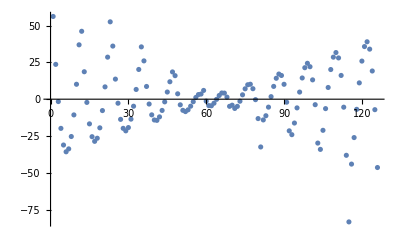

0.988956

```mathematica
regMinimaAnalysis["ParameterTable"]
residualArrayMinima=regMinimaAnalysis["FitResiduals"]
ListPlot[regMinimaAnalysis["FitResiduals"]]
regMinimaAnalysis["RSquared"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.498871 | 0.0447655 | 11.1441 | 3.10424×10^-20
ϵ | 0.00158732 | 0.0110333 | 0.143866 | 0.885848
σ | 0.193075 | 0.0104206 | 18.5283 | 5.30418×10^-37
ϵ^2 | -0.0000530054 | 0.000825407 | -0.0642173 | 0.948904
ϵ σ | -0.00021952 | 0.000692987 | -0.316773 | 0.751966
σ^2 | -0.0141745 | 0.000731635 | -19.3738 | 9.485×10^-39

{-0.148933,0.0567988,0.115129,0.0925049,0.0395721,-0.0151367,-0.0564223,-0.0761723,-0.0700136,-0.0355842,0.0283712,-0.150142,0.0558095,0.11436,0.0919547,0.0392414,-0.0152479,-0.0563139,-0.0758445,-0.0694662,-0.0348173,0.0293576,0.123694,-0.151244,0.0549263,0.113696,0.0915105,0.0390167,-0.015253,-0.0560996,-0.0754106,-0.0688128,-0.0339444,0.0304501,0.125006,-0.152241,0.054149,0.113138,0.0911723,0.0388981,-0.0151522,-0.0557792,-0.0748707,-0.0680534,-0.0329655,0.0316485,0.126424,-0.153132,0.0534778,0.112686,0.0909401,0.0388854,-0.0149453,-0.0553529,-0.0742248,-0.067188,-0.0318806,0.0329529,-0.153917,0.0529126,0.112341,0.0908139,0.0389787,-0.0146325,-0.0548205,-0.0734729,-0.0662166,-0.0306896,0.0343634,-0.154595,0.0524534,0.112101,0.0907938,0.0391781,-0.0142136,-0.0541821,-0.072615,-0.0651392,-0.0293927,0.0358799,0.131314,-0.155168,0.0521002,0.111967,0.0908796,0.0394835,-0.0136887,-0.0534377,-0.0716511,-0.0639557,-0.0279897,0.0375024,-0.155635,0.051853,0.11194,0.0910715,0.0398948,-0.0130578,-0.0525873,-0.0705812,-0.0626663,-0.0264808,0.0392308,-0.155996,0.0517118,0.112018,0.0913693,0.0404122,-0.0123209,-0.0516308,-0.0694052,-0.0612708,-0.0248658,0.0410654,0.137158,-0.15625,0.0516766,0.112202,0.0917732,0.0410356,-0.011478,-0.0505684,-0.0681233,-0.0597694,-0.0231448,0.0430059}

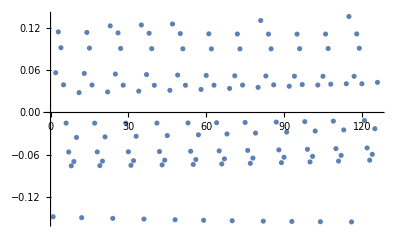

0.776545

```mathematica
regδforminAnalysis["ParameterTable"]
residualArrayδ=regδforminAnalysis["FitResiduals"]
ListPlot[regδforminAnalysis["FitResiduals"]]
regδforminAnalysis["RSquared"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -4.29194 | 0.0386227 | -111.125 | 7.32957×10^-123
ϵ | 0.00119782 | 0.0095193 | 0.125831 | 0.900076
σ | -0.808356 | 0.00899066 | -89.9107 | 5.94517×10^-112
ϵ^2 | -0.000039999 | 0.000712143 | -0.0561671 | 0.955302
ϵ σ | -0.000165654 | 0.000597894 | -0.277063 | 0.782208
σ^2 | -0.0106254 | 0.000631239 | -16.8326 | 2.22591×10^-33

{-0.138074,0.0697674,0.101296,0.0695751,0.0229793,-0.0188659,-0.0475491,-0.0591764,-0.0518101,-0.0244256,0.023546,-0.138986,0.0690209,0.100715,0.0691599,0.0227297,-0.0189498,-0.0474674,-0.058929,-0.051397,-0.0238469,0.0242904,0.0933426,-0.139818,0.0683544,0.100214,0.0688247,0.0225602,-0.0189537,-0.0473056,-0.0586016,-0.050904,-0.0231882,0.0251147,0.0943326,-0.14057,0.0677678,0.0997932,0.0685695,0.0224706,-0.0188776,-0.0470639,-0.0581942,-0.0503309,-0.0224494,0.0260191,0.0954026,-0.141242,0.0672613,0.0994523,0.0683943,0.0224611,-0.0187215,-0.0467421,-0.0577068,-0.0496779,-0.0216307,0.0270035,-0.141835,0.0668348,0.0991914,0.0682991,0.0225315,-0.0184855,-0.0463404,-0.0571394,-0.0489448,-0.020732,0.0280678,-0.142347,0.0664883,0.0990105,0.0682838,0.0226819,-0.0181694,-0.0458586,-0.056492,-0.0481317,-0.0197533,0.0292122,0.0990927,-0.142779,0.0662217,0.0989097,0.0683486,0.0229124,-0.0177733,-0.0452969,-0.0557646,-0.0472387,-0.0186946,0.0304366,-0.143131,0.0660352,0.0988888,0.0684934,0.0232228,-0.0172972,-0.0446551,-0.0549572,-0.0462656,-0.0175559,0.0317409,-0.143403,0.0659287,0.0989479,0.0687182,0.0236132,-0.0167411,-0.0439334,-0.0540698,-0.0452126,-0.0163372,0.0331253,0.103503,-0.143595,0.0659021,0.099087,0.0690229,0.0240837,-0.016105,-0.0431317,-0.0531024,-0.0440796,-0.0150385,0.0345896}

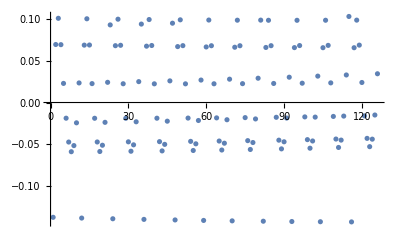

0.999524

```mathematica
regzforminAnalysis["ParameterTable"]
residualArrayz=regzforminAnalysis["FitResiduals"]
ListPlot[regzforminAnalysis["FitResiduals"]]
regzforminAnalysis["RSquared"]
```

```mathematica
residualArrayz[[2]]
```

0.0697674

```mathematica
ThreeDResArrayMinima={};
ThreeDResArrayδ={};
ThreeDResArrayz={};
Subϵ=0;
Subσ=0;
count=0;

For[n=0,n<=10,n++,

Subϵ++;
Subσ=0;

For[i=0,i<=10,i++,

count++;
Subσ++;

ThreeDResArrayMinima=AppendTo[ThreeDResArrayMinima,{Subϵ,Subσ,residualArrayMinima[[count]]}];
ThreeDResArrayδ=AppendTo[ThreeDResArrayδ,{Subϵ,Subσ,residualArrayδ[[count]]}];
ThreeDResArrayz=AppendTo[ThreeDResArrayz,{Subϵ,Subσ,residualArrayz[[count]]}];

]
]
(*Print[residualArrayMinima,"\n\n",residualArrayδ,"\n\n",residualArrayz]*)
Print[ThreeDResArrayMinima,"\n\n",ThreeDResArrayδ,"\n\n",ThreeDResArrayz]
```

{{1,1,56.2128},{1,2,23.6575},{1,3,-1.61667},{1,4,-19.8255},{1,5,-31.1476},{1,6,-35.744},{1,7,-33.767},{1,8,-25.3645},{1,9,-10.6824},{1,10,10.1347},{1,11,36.9431},{2,1,46.1434},{2,2,18.6455},{2,3,-2.18258},{2,4,-16.7724},{2,5,-25.4816},{2,6,-28.6317},{2,7,-26.5274},{2,8,-19.4649},{2,9,-7.73566},{2,10,8.37114},{2,11,28.568},{3,1,52.5683},{3,2,36.0823},{3,3,13.6419},{3,4,-2.74014},{3,5,-13.711},{3,6,-19.8072},{3,7,-21.511},{3,8,-19.2795},{3,9,-13.5569},{3,10,-4.78052},{3,11,6.61594},{4,1,20.2012},{4,2,35.5455},{4,3,26.0295},{4,4,8.64656},{4,5,-3.28934},{4,6,-10.6413},{4,7,-14.1244},{4,8,-14.382},{4,9,-12.0232},{4,10,-7.64052},{4,11,-1.81704},{5,1,4.86911},{5,2,11.8428},{5,3,18.531},{5,4,15.9851},{5,5,3.65963},{5,6,-3.83017},{5,7,-7.56321},{5,8,-8.43328},{5,9,-7.24455},{5,10,-4.75861},{5,11,-1.71581},{6,1,1.15481},{6,2,3.13063},{6,3,3.4928},{6,4,5.94912},{6,5,-1.31894},{6,6,-4.36265},{6,7,-4.47675},{6,8,-2.7338},{6,9,-0.0987864},{6,10,2.51437},{6,11,4.21725},{7,1,4.13502},{7,2,1.40051},{7,3,-4.84888},{7,4,-4.07855},{7,5,-6.28915},{7,6,-4.88678},{7,7,-1.38193},{7,8,2.97405},{7,9,7.05534},{7,10,9.79571},{7,11,10.1587},{8,1,7.12358},{8,2,-0.321256},{8,3,-13.1822},{8,4,-32.4623},{8,5,-14.0979},{8,6,-11.251},{8,7,-5.40254},{8,8,1.72125},{8,9,8.69025},{8,10,14.2178},{8,11,17.0854},{9,1,16.1085},{9,2,10.1205},{9,3,-2.03466},{9,4,-21.5072},{9,5,-24.1088},{9,6,-16.2045},{9,7,-5.90995},{9,8,4.83278},{9,9,14.4148},{9,10,21.3887},{9,11,24.3835},{10,1,22.0666},{10,2,13.1258},{10,3,-3.73971},{10,4,-29.8238},{10,5,-34.1114},{10,6,-21.1496},{10,7,-6.40899},{10,8,7.95268},{10,9,20.1477},{10,10,28.5679},{10,11,31.6899},{11,1,28.0331},{11,2,16.1394},{11,3,-5.43639},{11,4,-38.132},{11,5,-83.3804},{11,6,-44.1056},{11,7,-26.0864},{11,8,-6.89968},{11,9,11.0809},{11,10,25.889},{11,11,35.7554}}

{{1,1,-0.148933},{1,2,0.0567988},{1,3,0.115129},{1,4,0.0925049},{1,5,0.0395721},{1,6,-0.0151367},{1,7,-0.0564223},{1,8,-0.0761723},{1,9,-0.0700136},{1,10,-0.0355842},{1,11,0.0283712},{2,1,-0.150142},{2,2,0.0558095},{2,3,0.11436},{2,4,0.0919547},{2,5,0.0392414},{2,6,-0.0152479},{2,7,-0.0563139},{2,8,-0.0758445},{2,9,-0.0694662},{2,10,-0.0348173},{2,11,0.0293576},{3,1,0.123694},{3,2,-0.151244},{3,3,0.0549263},{3,4,0.113696},{3,5,0.0915105},{3,6,0.0390167},{3,7,-0.015253},{3,8,-0.0560996},{3,9,-0.0754106},{3,10,-0.0688128},{3,11,-0.0339444},{4,1,0.0304501},{4,2,0.125006},{4,3,-0.152241},{4,4,0.054149},{4,5,0.113138},{4,6,0.0911723},{4,7,0.0388981},{4,8,-0.0151522},{4,9,-0.0557792},{4,10,-0.0748707},{4,11,-0.0680534},{5,1,-0.0329655},{5,2,0.0316485},{5,3,0.126424},{5,4,-0.153132},{5,5,0.0534778},{5,6,0.112686},{5,7,0.0909401},{5,8,0.0388854},{5,9,-0.0149453},{5,10,-0.0553529},{5,11,-0.0742248},{6,1,-0.067188},{6,2,-0.0318806},{6,3,0.0329529},{6,4,-0.153917},{6,5,0.0529126},{6,6,0.112341},{6,7,0.0908139},{6,8,0.0389787},{6,9,-0.0146325},{6,10,-0.0548205},{6,11,-0.0734729},{7,1,-0.0662166},{7,2,-0.0306896},{7,3,0.0343634},{7,4,-0.154595},{7,5,0.0524534},{7,6,0.112101},{7,7,0.0907938},{7,8,0.0391781},{7,9,-0.0142136},{7,10,-0.0541821},{7,11,-0.072615},{8,1,-0.0651392},{8,2,-0.0293927},{8,3,0.0358799},{8,4,0.131314},{8,5,-0.155168},{8,6,0.0521002},{8,7,0.111967},{8,8,0.0908796},{8,9,0.0394835},{8,10,-0.0136887},{8,11,-0.0534377},{9,1,-0.0716511},{9,2,-0.0639557},{9,3,-0.0279897},{9,4,0.0375024},{9,5,-0.155635},{9,6,0.051853},{9,7,0.11194},{9,8,0.0910715},{9,9,0.0398948},{9,10,-0.0130578},{9,11,-0.0525873},{10,1,-0.0705812},{10,2,-0.0626663},{10,3,-0.0264808},{10,4,0.0392308},{10,5,-0.155996},{10,6,0.0517118},{10,7,0.112018},{10,8,0.0913693},{10,9,0.0404122},{10,10,-0.0123209},{10,11,-0.0516308},{11,1,-0.0694052},{11,2,-0.0612708},{11,3,-0.0248658},{11,4,0.0410654},{11,5,0.137158},{11,6,-0.15625},{11,7,0.0516766},{11,8,0.112202},{11,9,0.0917732},{11,10,0.0410356},{11,11,-0.011478}}

{{1,1,-0.138074},{1,2,0.0697674},{1,3,0.101296},{1,4,0.0695751},{1,5,0.0229793},{1,6,-0.0188659},{1,7,-0.0475491},{1,8,-0.0591764},{1,9,-0.0518101},{1,10,-0.0244256},{1,11,0.023546},{2,1,-0.138986},{2,2,0.0690209},{2,3,0.100715},{2,4,0.0691599},{2,5,0.0227297},{2,6,-0.0189498},{2,7,-0.0474674},{2,8,-0.058929},{2,9,-0.051397},{2,10,-0.0238469},{2,11,0.0242904},{3,1,0.0933426},{3,2,-0.139818},{3,3,0.0683544},{3,4,0.100214},{3,5,0.0688247},{3,6,0.0225602},{3,7,-0.0189537},{3,8,-0.0473056},{3,9,-0.0586016},{3,10,-0.050904},{3,11,-0.0231882},{4,1,0.0251147},{4,2,0.0943326},{4,3,-0.14057},{4,4,0.0677678},{4,5,0.0997932},{4,6,0.0685695},{4,7,0.0224706},{4,8,-0.0188776},{4,9,-0.0470639},{4,10,-0.0581942},{4,11,-0.0503309},{5,1,-0.0224494},{5,2,0.0260191},{5,3,0.0954026},{5,4,-0.141242},{5,5,0.0672613},{5,6,0.0994523},{5,7,0.0683943},{5,8,0.0224611},{5,9,-0.0187215},{5,10,-0.0467421},{5,11,-0.0577068},{6,1,-0.0496779},{6,2,-0.0216307},{6,3,0.0270035},{6,4,-0.141835},{6,5,0.0668348},{6,6,0.0991914},{6,7,0.0682991},{6,8,0.0225315},{6,9,-0.0184855},{6,10,-0.0463404},{6,11,-0.0571394},{7,1,-0.0489448},{7,2,-0.020732},{7,3,0.0280678},{7,4,-0.142347},{7,5,0.0664883},{7,6,0.0990105},{7,7,0.0682838},{7,8,0.0226819},{7,9,-0.0181694},{7,10,-0.0458586},{7,11,-0.056492},{8,1,-0.0481317},{8,2,-0.0197533},{8,3,0.0292122},{8,4,0.0990927},{8,5,-0.142779},{8,6,0.0662217},{8,7,0.0989097},{8,8,0.0683486},{8,9,0.0229124},{8,10,-0.0177733},{8,11,-0.0452969},{9,1,-0.0557646},{9,2,-0.0472387},{9,3,-0.0186946},{9,4,0.0304366},{9,5,-0.143131},{9,6,0.0660352},{9,7,0.0988888},{9,8,0.0684934},{9,9,0.0232228},{9,10,-0.0172972},{9,11,-0.0446551},{10,1,-0.0549572},{10,2,-0.0462656},{10,3,-0.0175559},{10,4,0.0317409},{10,5,-0.143403},{10,6,0.0659287},{10,7,0.0989479},{10,8,0.0687182},{10,9,0.0236132},{10,10,-0.0167411},{10,11,-0.0439334},{11,1,-0.0540698},{11,2,-0.0452126},{11,3,-0.0163372},{11,4,0.0331253},{11,5,0.103503},{11,6,-0.143595},{11,7,0.0659021},{11,8,0.099087},{11,9,0.0690229},{11,10,0.0240837},{11,11,-0.016105}}

```mathematica
ListPointPlot3D[ThreeDResArrayMinima]
```

-Graphics3D-

```mathematica
ListPointPlot3D[ThreeDResArrayδ]
```

-Graphics3D-

```mathematica
ListPointPlot3D[ThreeDResArrayz]
```

-Graphics3D-